```mathematica
X = {{0,1},{1,0}}
```

{{0,1},{1,0}}

```mathematica
Y={{0,-ⅈ},{ⅈ,0}}
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
M1 = MatrixExp[-ⅈ*(π+ϵ)/2*(X*Cos[ArcCos[-1/(4)]]+Y*Sin[ArcCos[-1/4]])]
Simplify[%]
```

{{-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2),1/8 (ⅈ-√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ-√15) ⅇ^((ⅈ ϵ)/2)},{1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2)+1/8 (ⅈ+√15) ⅇ^((ⅈ ϵ)/2),-1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2)+1/2 ⅈ ⅇ^((ⅈ ϵ)/2)}}

{{1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2) (-1+ⅇ^(ⅈ ϵ)),-1/8 (-ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2) (1+ⅇ^(ⅈ ϵ))},{1/8 (ⅈ+√15) ⅇ^(-(ⅈ ϵ)/2) (1+ⅇ^(ⅈ ϵ)),1/2 ⅈ ⅇ^(-(ⅈ ϵ)/2) (-1+ⅇ^(ⅈ ϵ))}}

```mathematica
M2 = MatrixExp[-ⅈ*2*(π+ϵ)/2(X*Cos[3*ArcCos[-1/4]]+Y*Sin[3*ArcCos[-1/4]])]
Simplify[%]
```

{{-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2,1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]+ⅈ Sin[3 ArcCos[-1/4]])},{1/2 ⅇ^(-ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]])-1/2 ⅇ^(ⅈ ϵ) (-Cos[3 ArcCos[-1/4]]-ⅈ Sin[3 ArcCos[-1/4]]),-1/2 ⅇ^(-ⅈ ϵ)-ⅇ^(ⅈ ϵ)/2}}

{{-1/2 ⅇ^(-ⅈ ϵ) (1+ⅇ^(2 ⅈ ϵ)),1/32 (11+3 ⅈ √15) ⅇ^(-ⅈ ϵ) (-1+ⅇ^(2 ⅈ ϵ))},{1/32 (11-3 ⅈ √15) ⅇ^(-ⅈ ϵ) (-1+ⅇ^(2 ⅈ ϵ)),-1/2 ⅇ^(-ⅈ ϵ) (1+ⅇ^(2 ⅈ ϵ))}}

```mathematica
Clear[θ]
MX = MatrixExp[-ⅈ*(θ+ϵ)/2*X]
Simplify[%]
```

{{Cos[ϵ/2+θ/2],-ⅈ Sin[ϵ/2+θ/2]},{-ⅈ Sin[ϵ/2+θ/2],Cos[ϵ/2+θ/2]}}

{{Cos[(ϵ+θ)/2],-ⅈ Sin[(ϵ+θ)/2]},{-ⅈ Sin[(ϵ+θ)/2],Cos[(ϵ+θ)/2]}}

```mathematica
BB1 = FullSimplify[onestate.M1.M2.M1.MX.zerostate]
```

{1/64 (-4 (13 ⅈ+√15+(-3 ⅈ+√15) Cos[ϵ]) Cos[θ/2] Sin[ϵ/2]^3+Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ]) Sin[θ/2])}

```mathematica
{1/64 (-4 (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Cos[π/2] Sin[ϵ/2]^3+Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ]) Sin[π/2])}
```

{1/64 Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ])}

```mathematica
Store=FullSimplify[{1/64 (-4 (13 ⅈ+√15+(-3 ⅈ+√15) Cos[ϵ]) Cos[π/2] Sin[ϵ/2]^3+Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ]) Sin[π/2])}*{1/64 (-4 (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Cos[π/2] Sin[ϵ/2]^3+Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ]) Sin[π/2])}]
```

{(Cos[ϵ/2]^2 (-1372 Cos[ϵ]+284 Cos[2 ϵ]+3 (715-12 Cos[3 ϵ]+Cos[4 ϵ])))/1024}

```mathematica
Series[Store,{ϵ,0,7}]
```

{1-(5 ϵ^6)/512+O[ϵ]^8}

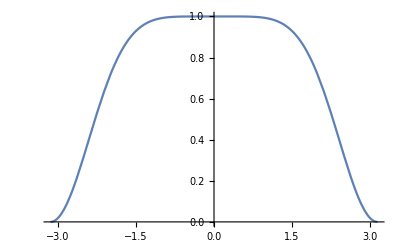

```mathematica
Plot[Store,{ϵ,-π,π}]
```

```mathematica
BB1Unitary =FullSimplify[ M1.M2.M1.MX]
```

{{-1/32 ⅈ (1/2 Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ]) Cos[θ/2]+2 (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3 Sin[θ/2]),1/64 (4 (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Cos[θ/2] Sin[ϵ/2]^3-Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ]) Sin[θ/2])},{1/64 (-4 (13 ⅈ+√15+(-3 ⅈ+√15) Cos[ϵ]) Cos[θ/2] Sin[ϵ/2]^3+Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ]) Sin[θ/2]),1/64 (Cos[ϵ/2] (89+3 ⅈ √15-4 ⅈ (-7 ⅈ+√15) Cos[ϵ]+(3+ⅈ √15) Cos[2 ϵ]) Cos[θ/2]+4 (-13+ⅈ √15+(3+ⅈ √15) Cos[ϵ]) Sin[ϵ/2]^3 Sin[θ/2])}}

```mathematica
θ=π
```

π

```mathematica
BB1Unitary = FullSimplify[BB1Unitary]
```

{{-1/16 ⅈ (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3,-1/64 Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ])},{1/64 Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ]),1/16 ⅈ (13 ⅈ+√15+(-3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3}}

```mathematica
BB1Transpose = Transpose[BB1Unitary]
```

{{-1/16 ⅈ (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3,1/64 Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ])},{-1/64 Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ]),1/16 ⅈ (13 ⅈ+√15+(-3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3}}

```mathematica
BB1ConjTranspose =Assuming[{Element[θ,Reals],Element[ϵ,Reals]}, Simplify[Conjugate[BB1Transpose]]]
```

{{1/16 ⅈ (13 ⅈ+√15+(-3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3,1/64 Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ])},{1/64 Cos[ϵ/2] (89 ⅈ-3 √15+4 (-7 ⅈ+√15) Cos[ϵ]-(-3 ⅈ+√15) Cos[2 ϵ]),-1/16 ⅈ (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3}}

```mathematica
FullSimplify[BB1Unitary.BB1ConjTranspose]
```

{{1,0},{0,1}}

```mathematica
Step1=BB1Unitary.zerostate
```

{{-1/16 ⅈ (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3},{1/64 Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ])}}

```mathematica
Step2=onestate.Step1
```

{1/64 Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ])}

```mathematica
Step3=Simplify[{1/64 Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ])}*{1/64 Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ])}]
```

{(Cos[ϵ/2]^2 (-1372 Cos[ϵ]+284 Cos[2 ϵ]+3 (715-12 Cos[3 ϵ]+Cos[4 ϵ])))/1024}

```mathematica
Series[Step3,{ϵ,0,8}]
```

{1-(5 ϵ^6)/512+(5 ϵ^8)/2048+O[ϵ]^9}

```mathematica
Plot[Step3,{ϵ,-π,π}]
```

-Graphics-

{{1/32 ⅈ Conjugate[1/2 Cos[ϵ/2] (-89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ]) Cos[θ/2]+2 (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Sin[ϵ/2]^3 Sin[θ/2]],1/64 Conjugate[-4 (13 ⅈ+√15+(-3 ⅈ+√15) Cos[ϵ]) Cos[θ/2] Sin[ϵ/2]^3+Cos[ϵ/2] (-89 ⅈ+3 √15-4 (-7 ⅈ+√15) Cos[ϵ]+(-3 ⅈ+√15) Cos[2 ϵ]) Sin[θ/2]]},{1/64 Conjugate[4 (-13 ⅈ+√15+(3 ⅈ+√15) Cos[ϵ]) Cos[θ/2] Sin[ϵ/2]^3-Cos[ϵ/2] (89 ⅈ+3 √15-4 (7 ⅈ+√15) Cos[ϵ]+(3 ⅈ+√15) Cos[2 ϵ]) Sin[θ/2]],1/64 Conjugate[Cos[ϵ/2] (89+3 ⅈ √15-4 ⅈ (-7 ⅈ+√15) Cos[ϵ]+(3+ⅈ √15) Cos[2 ϵ]) Cos[θ/2]+4 (-13+ⅈ √15+(3+ⅈ √15) Cos[ϵ]) Sin[ϵ/2]^3 Sin[θ/2]]}}

```mathematica
zerostate= {{1},{0}}
onestate={0,1}
```

{{1},{0}}

{0,1}